```mathematica
Mammalian Circadian Clock Model DD
                           				Jaekyoung Kim Daniel B. Forger
```

```mathematica
(*Initial Condition for the multi-state variable x[j][k][l][m][n]*)
Init1={{{{{{0.},{0.3420612363991834}},{{0.},{8.179771245758342}}},{{{50.57941320972072},{0.}},{{3.084858510765489},{0.}}},{{{0.0985802410460628},{0.}},{{1.3084555441370038},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{41.165766704888945},{0.}},{{0.015608382491794207},{8.720885301950966}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{46.57213430901654},{0.}},{{0.0031953005375601647},{1.36799289498887}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.42289800101916825},{0.}},{{0.},{0.}}},{{{1.0925402835728917},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.0018172208474570813},{0.}},{{0.000051969832456607834},{0.005122234469530184}}},{{{0.1065745913827944},{0.}},{{0.0008330734700784042},{0.0566635532527744}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.0032917376286310976},{0.}},{{0.000014996030154730353},{0.005431344430745013}}},{{{0.08769094840691996},{0.}},{{0.0003337441556398164},{0.05489271181066792}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.0034854600146215606},{0.}},{{0.00001543121168014226},{0.005104574272816484}}},{{{0.09387578379334667},{0.}},{{0.0003536110985068703},{0.053591842109765024}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.9143646209767509},{0.}},{{0.},{0.}}},{{{0.6640388319296585},{0.}},{{0.},{0.}}},{{{0.02261620526647949},{0.}},{{0.},{0.}}},{{{0.024153127001179508},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}},{{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}},{{{0.},{0.}},{{0.},{0.}}}}},{{{{{0.003566426542717158},{0.}},{{0.000019446948491991687},{0.0009593633157572193}}},{{{0.25844220368442533},{0.}},{{0.0009853861095753967},{0.024999109498991166}}},{{{0.0001571030498997009},{0.}},{{0.000011241988156917215},{0.0013233693432189286}}},{{{0.010591367829307969},{0.}},{{0.00023061993448538233},{0.025310956921162836}}}},{{{{0.003906943572357614},{0.}},{{0.000013488201348952268},{0.0008093091845965769}}},{{{0.124712274740282},{0.}},{{0.0004168131259404268},{0.014891880773138683}}},{{{0.00018883274230441384},{0.}},{{1.7997916251845195*^-6},{0.0010929293853399464}}},{{{0.005847694864620672},{0.}},{{0.00004358370050515716},{0.01661068549366629}}}},{{{{0.0042845356189285195},{0.}},{{0.000014771592378319274},{0.0008613198533091311}}},{{{0.1376958595595994},{0.}},{{0.00045981124781785865},{0.01603487525209985}}},{{{0.00020679957949088886},{0.}},{{1.9401844427852306*^-6},{0.0011515995567390796}}},{{{0.006446263165149906},{0.}},{{0.00004763488605319544},{0.01770213916985296}}}}},{{{{{0.005698064997206092},{0.}},{{0.00019083191864807688},{0.05668344375489035}}},{{{0.028756909151433502},{0.}},{{0.00041383171976532257},{0.04946506549670688}}},{{{0.0041450474340475356},{0.}},{{0.0003862225731469661},{0.12446417224048362}}},{{{0.0074079613548572055},{0.}},{{0.0006543776273979713},{0.10408853180005757}}}},{{{{0.006669740144184649},{0.}},{{0.00002542209112423298},{0.004845243944628116}}},{{{0.0828541248216783},{0.}},{{0.0002945640707027717},{0.032357261166932494}}},{{{0.0012141988050762562},{0.}},{{0.000011508013921347713},{0.009768583317773775}}},{{{0.008747399124363007},{0.}},{{0.00007984935519557792},{0.06078778560702874}}}},{{{{0.007063852050803612},{0.}},{{0.00002642920327460206},{0.004422509243751679}}},{{{0.08527034138444498},{0.}},{{0.00030090634602644245},{0.030114250838098423}}},{{{0.0013264050530040427},{0.}},{{0.000011249707819832738},{0.00878990944810083}}},{{{0.009150500594118106},{0.}},{{0.00007786053056329725},{0.05558596503417361}}}}},{{{{{0.0007928248680611883},{0.}},{{0.000025780353419672163},{0.0033458239867342923}}},{{{0.0274124885839697},{0.}},{{0.00038549841376936617},{0.05899370416043617}}},{{{0.0001255123171657433},{0.}},{{0.00004997690057380442},{0.007351856000655174}}},{{{0.005502328645107724},{0.}},{{0.0006319867772882921},{0.12768021452441894}}}},{{{{0.0025210125949368953},{0.}},{{0.000010077905400078566},{0.0024810297377193245}}},{{{0.05812325888303372},{0.}},{{0.00020742923534716493},{0.023913749818730998}}},{{{0.00030530718232012633},{0.}},{{4.902173374599667*^-6},{0.005219487814016039}}},{{{0.007539434826295608},{0.}},{{0.00006395851528373895},{0.04714353907964912}}}},{{{{0.0025977211835363366},{0.}},{{0.00001017089395981654},{0.002248072566075126}}},{{{0.060247906870995155},{0.}},{{0.00021344857807776635},{0.022578312737100606}}},{{{0.0003200670130454894},{0.}},{{4.603722758559816*^-6},{0.004701002286841585}}},{{{0.007971833585551605},{0.}},{{0.00006352606272272561},{0.04407940585392828}}}}}};

(*Initial Condition for the single-state variable*)
Init2={0.21004770358705036,0.7879547112081645,1.1383721663365372,3.760854376307055,1.095465622771389,12.37354665811613,4.470535676137161,4.189465465043962,0.5791077386453771,8.349625799238817,1.4116789475658296,35.184199298572295,8.56043138049844,23.77410578150899,0.5893077833141493,0.40424721668584945,48.09767559849965,31.869023309234613,161.14372712932516,123.95046120625604,467.84444843738225,0.1932885142503498,58.23913168018502,0.03971373557862615,19.06619007243528,0.5999649539384736,0.39359004606153003,0,0.11012045498612394,67.61745646537098,0,0,6.5815025579914295,0.4162165798701546,0.5585648324701572,0.,0.25595982171319526,0.5203673130406197,0.19388642676798773,0.8044041532454284};

Init3={0.0,0.0,0.0};
```

```mathematica
(*Transcription Rate*)
trPo=25.9201;trPt=44.854;trRo=23.0747;trRt=39.9409;trB=46.1038;trRev=102.92299999999999;trNp=0.3297485941817571;

(*Translation Rate*)
tlp=1.81031;tlr=5.03882;tlb=0.530436;tlrev=8.90744;tlc=4.645890;tlnp=1.25099;

(*Binding/Unbinding Rate between Proteins*)
agp=1.3962;dg=2.93521;ac=0.0456572;dc=0.108072;ar=0.0235285;dr=0.605268;cbin=0.0454894;uncbin=7.27215;
bbin=6.92686;unbbin=0.130196;cbbin=6.59924;uncbbin=0.304176;ag=0.162392;

(*Binding/Unbinding Rate on Promoters*)
bin=6.97166;unbin=0.255032;binrev=0.0120525;unbinrev=10.9741;binr=6.15445;unbinr=2.91009;binc=0.280863;
unbinc=0.00886752;binrevb=0.00626588;unbinrevb=5.30559;

(*Translocation Rate*)
tmc=0.16426;tmcrev=9.2631;nl=0.643086;ne=0.0269078;nlrev=9.63702;nerev=0.0152514;lne=0.594609;nlbc=5.26501;


(*Phosphorylation Rate*)
hoo=0.527453;hto=2.45584;phos=0.291429;

(*Light Effet*)
lono=0.205813;lont=0.396392;lta=0.693695*(500/9500)^0.0451246;ltb=0.013;

(*GSK3b Activity*)
trgto=0.644602;ugto=0.0625777;

(*Ratio beteeen Cytoplasm and Nucleus*)
Nf=3.35063;


(*Degradation Rate*)
up=3.537;uro=0.17491;urt=0.481895;umNp=0.369493;
umPo=0.76696222;umPt=0.58891980;umRo=0.40342526000000006;umRt=0.45554418;ub=0.018800209999999998;uc=0.025165115999999998;
ubc=0.34882936000000003;upu=0.0700322;urev=1.6487614725107194;uprev=0.5173026723236928;umB=0.7954019999999999;umRev=1.510194;

(*Newly Added Reactions*)
binp=bbin;unbinp=1000*unbin;unbinrp=1000*unbinr;unbincp=1000*unbinc;
```

```mathematica
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];
```

```mathematica
Differential Equations Solver
```

```mathematica
athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,480},MaxSteps->100000,MaxStepSize->0.1];
wt=Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,0,96,0.01}];
```

```mathematica
Plot
```

```mathematica
measureperiod[timeseries_]:=Module[{period},(If[Length[FindPeaks[timeseries]]>2,If[1+FindPeaks[-timeseries][[-2]][[2]]/FindPeaks[timeseries][[-2]][[2]]>0.1,period=0.01*(FindPeaks[timeseries][[-2]][[1]]-FindPeaks[timeseries][[-3]][[1]]),period=0],period=0])];
```

```mathematica
Print[measureperiod[Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,240,480,0.01}]]];
```

23.73

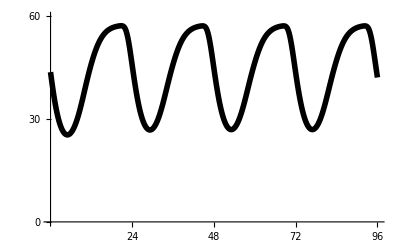

```mathematica
ListPlot[Table[{t,((MnB[t]+McB[t])/.qrt)[[1]]},{t,0,96,0.1}],Joined->True,PlotRange->{{0,96},{0,60}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Black,Thickness[0.01]],Ticks->{{24,48,72,96},{0,30,60}}]
```

WT

```mathematica
Equations
```

```mathematica
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+0-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];
```

```mathematica
Differential Equations Solver
```

```mathematica
athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,240},MaxSteps->100000,MaxStepSize->0.1];
clockKO=Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,96,192,0.01}];
```

```mathematica
Plot
```

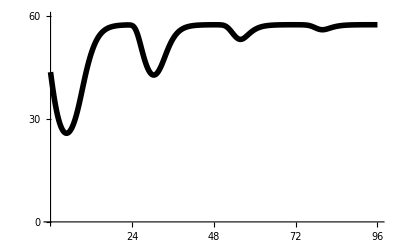

```mathematica
ListPlot[Table[{t,((MnB[t]+McB[t])/.qrt)[[1]]},{t,0,96,0.1}],Joined->True,PlotRange->{{0,96},{0,60}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Black,Thickness[0.01]],Ticks->{{24,48,72,96},{0,30,60}}]
```

CLOCK KO

```mathematica
Equations
```

```mathematica
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==0*tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];
```

```mathematica
Differential Equations Solver
```

```mathematica
athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,240},MaxSteps->100000,MaxStepSize->0.1];
bmal1KO=Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,96,192,0.01}];
```

```mathematica
Plot
```

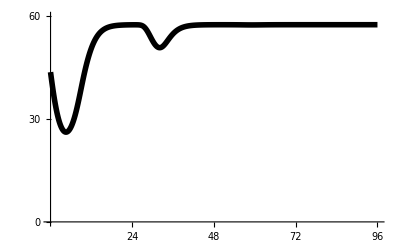

```mathematica
ListPlot[Table[{t,((MnB[t]+McB[t])/.qrt)[[1]]},{t,0,96,0.1}],Joined->True,PlotRange->{{0,96},{0,60}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Black,Thickness[0.01]],Ticks->{{24,48,72,96},{0,30,60}}]
```

BMAL1 KO

```mathematica
measureperiod[timeseries_]:=Module[{period},(If[Length[FindPeaks[timeseries]]>2,If[1+FindPeaks[-timeseries][[-2]][[2]]/FindPeaks[timeseries][[-2]][[2]]>0.1,period=0.01*(FindPeaks[timeseries][[-2]][[1]]-FindPeaks[timeseries][[-3]][[1]]),period=0],period=0])];
```

23.82

23.11

22.68

22.52

22.45

22.41

22.4

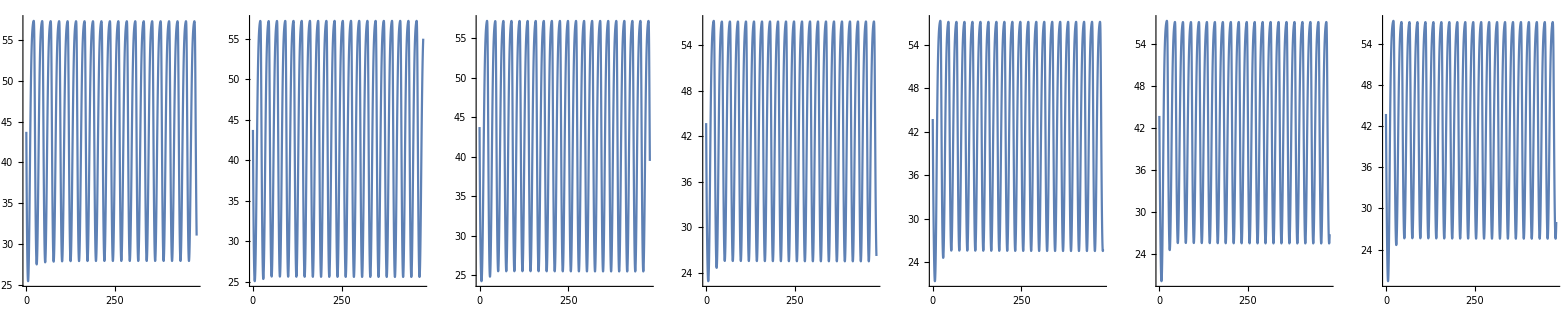

```mathematica
listCl={4,8,16,32,64,128,256};imglist={};tslist={};
For[i=1,i≤Length[listCl],i++,
overCl=listCl[[i]];
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+overCl-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*(G[t])*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];


athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,480},MaxSteps->100000,MaxStepSize->0.01];
Print[measureperiod[Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,240,480,0.01}]]];imglist=Join[imglist,{Plot[(MnB[t]+McB[t])/.qrt,{t,0,480},PlotRange->{{432,480},{0,All}}]}];tslist=Join[tslist,{Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,0,96,0.01}]}]];GraphicsGrid[{imglist}]
```

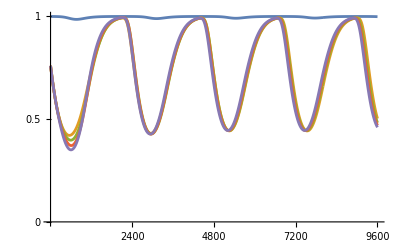

```mathematica
ListPlot[Join[{clockKO/Max[clockKO]},tslist[[3;;6]]/Max[clockKO]],Joined->True,Ticks->{{2400,4800,7200,9600},{0,0.5,1}},PlotRange->{{0,9600},{0,1}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.005]]
```

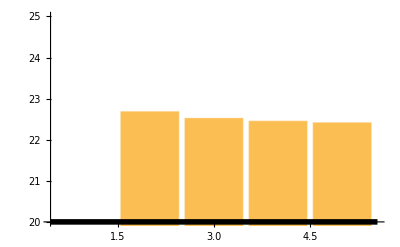

```mathematica
BarChart[{0,22.68,22.52,22.45,22.41},Ticks->{Automatic,{20,21,22,23,24,25}},AxesStyle->Directive[Black,Thickness[0.01]],PlotRange->{20,25}]
```

CLOCK KO + CLOCK overexpression

23.91

24.48

24.64

24.7

24.72

24.73

24.73

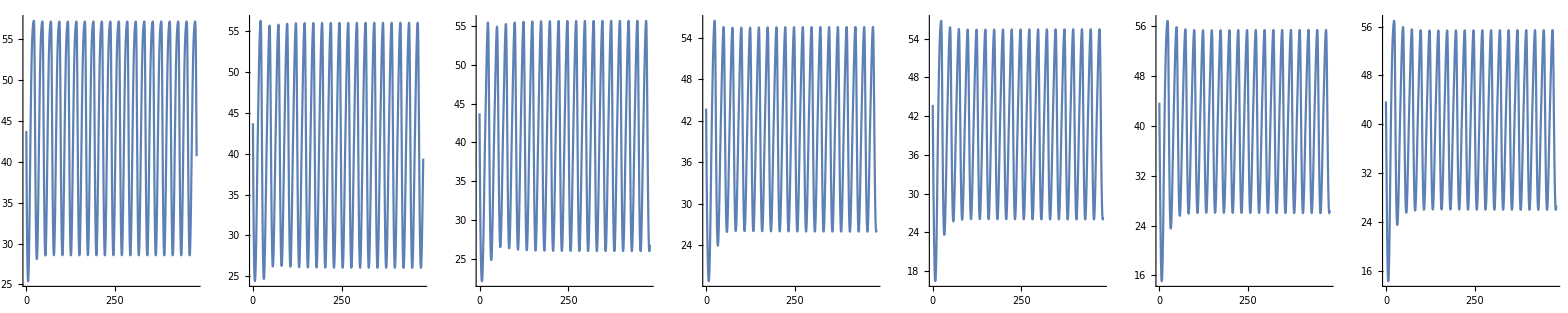

```mathematica
listB={4,8,16,32,64,128,256};imglist={};tslist={};
For[i=1,i≤Length[listB],i++,
overB=listB[[i]];
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==overB-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];


athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,480},MaxSteps->100000,MaxStepSize->0.01];
Print[measureperiod[Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,240,480,0.01}]]];imglist=Join[imglist,{Plot[(MnB[t]+McB[t])/.qrt,{t,0,480},PlotRange->{{432,480},{0,All}}]}];tslist=Join[tslist,{Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,0,96,0.01}]}]];GraphicsGrid[{imglist}]
```

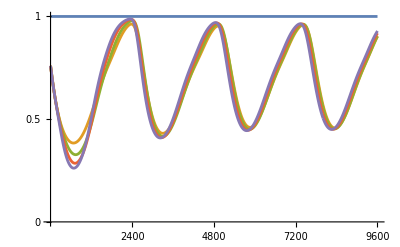

```mathematica
ListPlot[Join[{bmal1KO/Max[bmal1KO]},tslist[[3;;6]]/Max[bmal1KO]],Joined->True,Ticks->{{2400,4800,7200,9600},{0,0.5,1}},PlotRange->{{0,9600},{0,1}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.005]]
```

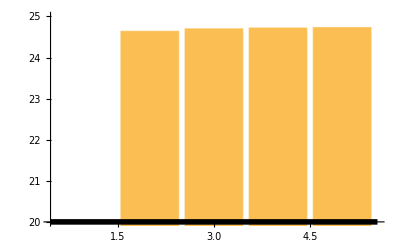

```mathematica
BarChart[{0,24.64,24.70,24.72,24.73},Ticks->{Automatic,{20,21,22,23,24,25}},AxesStyle->Directive[Black,Thickness[0.01]],PlotRange->{20,25}]
```

BMAL1 KO + BMAL1 overexpression

22.53

22.41

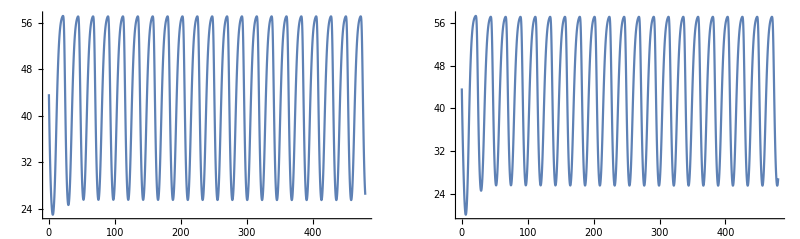

```mathematica
listCl={26,128};imglist={};tslist={};
For[i=1,i≤Length[listCl],i++,
overCl=listCl[[i]];
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+overCl+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*(G[t])*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];


athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,480},MaxSteps->100000,MaxStepSize->0.01];
Print[measureperiod[Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,240,480,0.01}]]];imglist=Join[imglist,{Plot[(MnB[t]+McB[t])/.qrt,{t,0,480},PlotRange->{{432,480},{0,All}}]}];tslist=Join[tslist,{Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,0,96,0.01}]}]];GraphicsGrid[{imglist}]
```

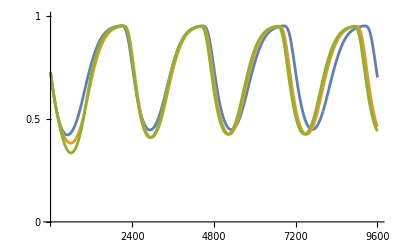

```mathematica
ListPlot[Join[{wt/60},tslist/60],Joined->True,Ticks->{{2400,4800,7200,9600},{0,0.5,1}},PlotRange->{{0,9600},{0,1}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.005]]
```

CLOCK WT + CLOCK overexpression

24.69

24.72

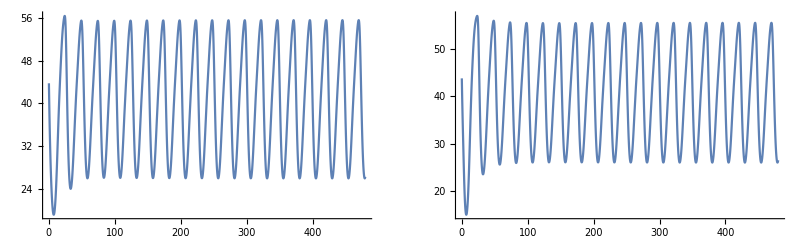

```mathematica
listB={26,128};imglist={};tslist={};
For[i=1,i≤Length[listB],i++,
overB=listB[[i]];
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==overB+tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];


athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,480},MaxSteps->100000,MaxStepSize->0.01];
Print[measureperiod[Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,240,480,0.01}]]];imglist=Join[imglist,{Plot[(MnB[t]+McB[t])/.qrt,{t,0,480},PlotRange->{{432,480},{0,All}}]}];tslist=Join[tslist,{Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,0,96,0.01}]}]];GraphicsGrid[{imglist}]
```

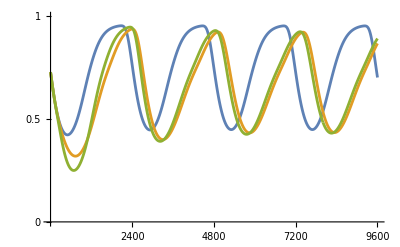

```mathematica
ListPlot[Join[{wt/60},tslist/60],Joined->True,Ticks->{{2400,4800,7200,9600},{0,0.5,1}},PlotRange->{{0,9600},{0,1}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.005]]
```

BMAL1 WT + BMAL1 overexpression

0

0

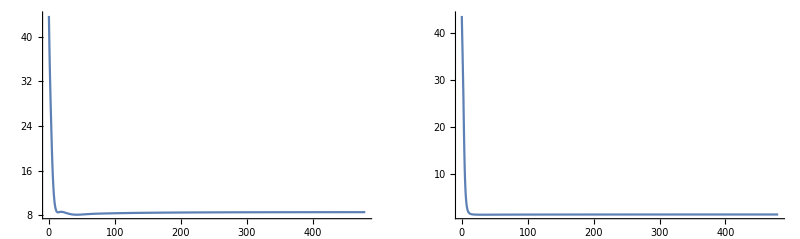

```mathematica
listBC={26,128};imglist={};tslist={};
For[i=1,i≤Length[listB],i++,
overBC=listBC[[i]];
(*Equstions for single-state variables*)
aone={
(*E-box activity*)
GR'[t]==bin*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-G[t]-GR[t]-GP[t])-unbin*GR[t],
G'[t]==bin*x[0][0][0][1][1][t]*(1-G[t]-GR[t]-GP[t])-unbin*G[t],
GrR'[t]==binr*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*GrR[t],
Gr'[t]==binr*x[0][0][0][1][1][t]*(1-Gr[t]-GrR[t]-GrP[t])-unbinr*Gr[t],
GcR'[t]==binc*(Sum[x[0][kk][0][1][1][t],{kk,1,2}])*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*GcR[t],
Gc'[t]==binc*x[0][0][0][1][1][t]*(1-Gc[t]-GcR[t]-GcP[t])-unbinc*Gc[t],

GP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(G[t]+GR[t])-unbinp*GP[t],GrP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gr[t]+GrR[t])-unbinrp*GrP[t],GcP'[t]==binp*(Sum[x[jj][kk][ll][1][0][t],{jj,1,6},{kk,0,0},{ll,0,3}])*(Gc[t]+GcR[t])-unbincp*GcP[t],

(*RORE activity*)
GBR'[t]==binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]-unbinrev*GBR[t],
GB'[t]==-binrev*(revn[t]+revng[t]+revngp[t]+revnp[t])*GB[t]+unbinrev*GBR[t],
GBRb'[t]==binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]-unbinrevb*GBRb[t],
GBb'[t]==-binrevb*(revn[t]+revng[t]+revngp[t]+revnp[t])*GBb[t]+unbinrevb*GBRb[t],

(*Transcription*)
MnPo'[t]==trPo*(G[t])-tmc*MnPo[t]-umPo*MnPo[t],McPo'[t]==tmc*MnPo[t]-umPo*McPo[t],
MnPt'[t]==trPt*(G[t])-tmc*MnPt[t]-umPt*MnPt[t],McPt'[t]==tmc*MnPt[t]-umPt*McPt[t],
MnRt'[t]==trRt*(Gc[t])-tmc*MnRt[t]-umRt*MnRt[t],McRt'[t]==tmc*MnRt[t]-umRt*McRt[t],
MnRev'[t]==trRev*x[0][0][0][1][1][t]*(Gr[t])-tmcrev*MnRev[t]-umRev*MnRev[t],
McRev'[t]==tmcrev*MnRev[t]-umRev*McRev[t],
MnRo'[t]==trRo*(G[t])*GB[t]-tmc*MnRo[t]-umRo*MnRo[t],
McRo'[t]==tmc*MnRo[t]-umRo*McRo[t],
MnB'[t]==trB*GBb[t]-tmc*MnB[t]-umB*MnB[t],
McB'[t]==tmc*MnB[t]-umB*McB[t],
MnNp'[t]==trNp*GB[t]-tmc*MnNp[t]-umNp*MnNp[t],
McNp'[t]==tmc*MnNp[t]-umNp*McNp[t],

(*Secondary Feedback Loop*)
B'[t]==overBC+tlb*McB[t]-cbin*B[t]*Cl[t]+uncbin*BC[t]-ub*B[t],
Cl'[t]==overBC+tlnp*McNp[t]+tlc-cbin*B[t]*Cl[t]+uncbin*BC[t]-uc*Cl[t],
BC'[t]==cbin*B[t]*Cl[t]-uncbin*BC[t]-phos*BC[t]-ubc*BC[t],cyrev'[t]==tlrev*McRev[t]-(nlrev+urev)*cyrev[t]-ag*cyrev[t]*(x[0][0][2][0][0][t])+nerev*revn[t]+dg*cyrevg[t],revn'[t]==-(nerev+urev)*revn[t]-ag*Nf*revn[t]*(x[0][0][2][1][0][t])+nlrev*cyrev[t]+dg*(revng[t]),cyrevg'[t]==ag*cyrev[t]*x[0][0][2][0][0][t]-(dg+gto[t]+urev+nlrev)*cyrevg[t]+nerev*revng[t],revng'[t]==ag*Nf*revn[t]*x[0][0][2][1][0][t]-(dg+gto[t]+urev+nerev)*revng[t]+nlrev*cyrevg[t],
cyrevgp'[t]==gto[t]*cyrevg[t]-(dg+uprev+nlrev)*cyrevgp[t]+nerev*revngp[t],
revngp'[t]==gto[t]*revng[t]-(dg+uprev+nerev)*revngp[t]+nlrev*cyrevgp[t],
cyrevp'[t]==dg*(cyrevgp[t])-(uprev+nlrev)*cyrevp[t]+nerev*revnp[t],
revnp'[t]==dg*(revngp[t])-(uprev+nerev)*revnp[t]+nlrev*cyrevp[t],

(*Activity of GSK3b*)
gto'[t]==trgto*G[t]*GB[t]-ugto*gto[t]};

(*Equstions for multi-state variables*)
atwo=Flatten[Table[x[j][k][l][m][n]'[t]==

(*Trnaslation*)
If[(j==1)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPo[t],0]+
If[(j==3)&&(k==0)&&(l==0)&&(m==0)&&(n==0),tlp*McPt[t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==0)&&(n==0),tlr*McRo[t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==0)&&(n==0),tlr*McRt[t],0]+


(*PER-CRY Binidng/Unbinidng*)
If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6)),-ar*If[m==1,Nf,1]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+
If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(n==0),-ar*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(n==0),ar*If[m==1,Nf,1]*x[0][k][0][m][n][t]*x[j][0][l][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==1)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][0][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][n][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==0),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][1][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][n][t]*x[0][k][0][m][0][t]-dr*x[j][k][l][m][n][t],0]+If[(k==0)&&(n==0)&&((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[0][kk][0][m][1][t],{kk,1,2}]+dr*Sum[x[j][kk][l][m][1][t],{kk,1,2}],0]+If[(j==0)&&((k==1)||(k==2))&&(l==0)&&(m==1)&&(n==1),-ar*Nf*x[j][k][l][m][n][t]*Sum[x[jj][0][ll][m][0][t],{jj,{2,4,5,6}},{ll,0,3}]+dr*Sum[x[jj][k][ll][m][n][t],{jj,{2,4,5,6}},{ll,0,3}],0]+
If[((j==2)||(j==4)||(j==5)||(j==6))&&((k==1)||(k==2))&&(m==1)&&(n==1),ar*Nf*x[j][0][l][m][0][t]*x[0][k][0][m][1][t]-dr*x[j][k][l][m][n][t],0]+

(*PER-CKI Binidng/Unbinidng*)
If[(l==0)&&(j>0)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][0][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][0][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(l==0)&&(j>0)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][1][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][0][m][1][t],{jj,1,6},{kk,0,2}]+dc*Sum[x[jj][kk][l][m][1][t],{jj,1,6},{kk,0,2}],0]+
If[(j>0)&&(l==1)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][0][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),-ac*If[m==1,Nf,1]*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][0][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][0][t],{jj,3,6},{kk,0,2}],0]+If[(j>2)&&(l==3)&&(n==0),ac*If[m==1,Nf,1]*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+If[(j>2)&&(l==2)&&(m==1)&&(n==1),-ac*Nf*x[j][k][l][m][n][t]*x[0][0][1][m][0][t]+dc*x[j][k][3][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(m==1)&&(n==0),-ac*Nf*x[j][k][l][m][n][t]*Sum[x[jj][kk][2][m][1][t],{jj,3,6},{kk,0,2}]+dc*Sum[x[jj][kk][3][m][1][t],{jj,3,6},{kk,0,2}],0]+
If[(j>2)&&(l==3)&&(m==1)&&(n==1),ac*Nf*x[0][0][1][m][0][t]*x[j][k][2][m][n][t]-dc*x[j][k][l][m][n][t],0]+

(*PER-GSK3b Binidng/Unbinidng*)
If[(j>2)&&((l==0)||(l==1)),-If[m==1,Nf,1]*agp*x[j][k][l][m][n][t]*x[0][0][2][m][0][t]+dg*x[j][k][l+2][m][n][t],0]+If[(j==0)&&(k==0)&&(l==2)&&(n==0),-If[m==1,Nf,1]*agp*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,0,1},{nn,0,1}]*x[j][k][l][m][n][t]+dg*Sum[x[jj][kk][ll][m][nn][t],{jj,3,6},{kk,0,2},{ll,2,3},{nn,0,1}],0]+If[(j>2)&&((l==2)||(l==3)),If[m==1,Nf,1]*agp*x[j][k][l-2][m][n][t]*x[0][0][2][m][0][t]-dg*x[j][k][l][m][n][t],0]+

(*PER-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j>0)&&(m==1)&&(n==0),-bbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+unbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-bbin*Nf*Sum[x[jj][kk][ll][m][0][t],{jj,1,6},{kk,0,2},{ll,0,3}]*x[j][k][l][m][n][t]+unbbin*Sum[x[jj][kk][ll][m][n][t],{jj,1,6},{kk,0,2},{ll,0,3}],0]+If[(j>0)&&(m==1)&&(n==1),bbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-unbbin*x[j][k][l][m][n][t],0]+

(*CRY-BMAL1-CLOCK/NPAS2 Binding/Unbinding*)
If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==0),-cbbin*Nf*x[j][k][l][m][n][t]*x[0][0][0][m][1][t]+uncbbin*x[j][k][l][m][1][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),-cbbin*Nf*Sum[x[0][kk][0][m][0][t],{kk,1,2}]*x[j][k][l][m][n][t]+uncbbin*Sum[x[0][kk][0][m][n][t],{kk,1,2}],0]+If[(j==0)&&(k>0)&&(l==0)&&(m==1)&&(n==1),cbbin*Nf*x[j][k][l][m][0][t]*x[0][0][0][m][n][t]-uncbbin*x[j][k][l][m][n][t],0]+

(*REV-ERBs-GSK3b Binding/Unbinding*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),-ag*cyrev[t]*x[j][k][l][m][n][t]+(dg)*cyrevg[t]+(dg)*cyrevgp[t],0]+If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),-ag*Nf*revn[t]*x[j][k][l][m][n][t]+(dg)*revng[t]+(dg)*revngp[t],0]+


(*PER Binding Protiens Subcellular Translocation*)
If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==1),-ne*If[(n==0),1,0]*x[j][k][l][m][n][t]+If[(n==0),1,0]*nl*x[j][k][l][0][n][t],0]+If[((j==2)||(j==4)||(j==5)||(j==6))&&(m==0),ne*If[(n==0),1,0]*x[j][k][l][1][n][t]-If[(n==0),1,0]*nl*x[j][k][l][m][n][t],0]+

(*BMAL1-CLOCK/NPAS2 Subcellular Translocation*)
If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),nlbc*x[j][k][l][0][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),-nlbc*x[j][k][l][m][n][t],0]+

(*Kinase Subcellular Translocation*)
If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==1)&&(n==0),-lne*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&((l==1)||(l==2))&&(m==0)&&(n==0),lne*x[j][k][l][1][n][t],0]+

(*PER Phosphorylation with CKI*)
If[((j==1))&&(l==1)&&(k==0)&&(m==0)&&(n==0),-hoo*x[j][k][l][m][n][t],0]+
If[((j==2))&&(l==1)&&(k==0)&&(m==0)&&(n==0),+hoo*x[1][k][l][m][n][t],0]+
If[((j==3)||(j==5))&&((l==1)||(l==3))&&(k==0),-hto*x[j][k][l][m][n][t],0]+
If[((j==4)||(j==6))&&((l==1)||(l==3))&&(k==0),hto*x[j-1][k][l][m][n][t],0]+

(*PER2 Phosphorylation with GSK3b*)
If[((j==3)||(j==4))&&((l==2)||(l==3)),-gto[t]*x[j][k][l][m][n][t],0]+
If[((j==5)||(j==6))&&((l==2)||(l==3)),gto[t]*x[j-2][k][l][m][n][t],0]+

(*BMAL-CLCOK/NPAS2 Phosphorylation with GSK3b*)

If[(j==0)&&(k==0)&&(l==0)&&(m==0)&&(n==1),phos*BC[t],0]+

(*CRY Degradation*)
If[(j==0)&&(k==1)&&(l==0)&&(n==0),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(n==0),-urt*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==1)&&(l==0)&&(m==1)&&(n==1),-uro*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==2)&&(l==0)&&(m==1)&&(n==1),-urt*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==0)&&(m==1)&&(n==1),uro*x[j][1][l][m][n][t]+urt*x[j][2][l][m][n][t],0]+

(*PER Degradation*)
If[((j==1)||(j==3)||(j==5))&&(k==0),-If[(m==0)&&(n==1),0,1]*upu*x[j][k][l][m][n][t],0]+If[((j==2)||(j==4)||(j==6))&&(k==0),-If[(m==0)&&(n==1),0,1]*up*x[j][k][l][m][n][t],0]+If[(j==0)&&(k==0)&&(l==1)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{nn,0,1},{ll,1,3,2}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{nn,0,1},{ll,1,3,2}],0]+
If[(j==0)&&(k==0)&&(l==2)&&(n==0),up*Sum[x[jj][0][ll][m][nn][t],{jj,2,6,2},{ll,2,3},{nn,0,1}]+upu*Sum[x[jj][0][ll][m][nn][t],{jj,1,5,2},{ll,2,3},{nn,0,1}],0]+If[(j==0)&&(k==0)&&(l==0)&&(n==1)&&(m==1),up*Sum[x[jj][0][ll][m][n][t],{jj,2,6,2},{ll,0,3}]+upu*Sum[x[jj][0][ll][m][n][t],{jj,1,5,2},{ll,0,3}],0]+

(*BMAL1-CLOCK/NPAS2 Degradation*)
If[(j>0)&&(k==0)&&(m==1)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j==0)&&(k==0)&&(l==0)&&(n==1),-ubc*x[j][k][l][m][n][t],0]+
If[(j>0)&&(k==0)&&(m==1)&&(n==0),ubc*x[j][k][l][m][1][t],0]+

(*REV-ERBS Degradation*)
If[(j==0)&&(k==0)&&(l==2)&&(m==0)&&(n==0),urev*cyrevg[t]+uprev*cyrevgp[t],0]+
If[(j==0)&&(k==0)&&(l==2)&&(m==1)&&(n==0),urev*revng[t]+uprev*revngp[t],0],
{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];


athree={G[0]==Init2[[1]],GR[0]==Init2[[2]],gto[0]==Init2[[3]],MnRo[0]==Init2[[4]],McRo[0]==Init2[[5]],MnRt[0]==Init2[[6]],McRt[0]==Init2[[7]],MnPo[0]==Init2[[8]],McPo[0]==Init2[[9]],MnPt[0]==Init2[[10]],McPt[0]==Init2[[11]],MnB[0]==Init2[[12]],McB[0]==Init2[[13]],B[0]==Init2[[14]],GBb[0]==Init2[[15]],GBRb[0]==Init2[[16]],Cl[0]==Init2[[17]],MnRev[0]==Init2[[18]],McRev[0]==Init2[[19]],cyrev[0]==Init2[[20]],revn[0]==Init2[[21]],cyrevg[0]==Init2[[22]],revng[0]==Init2[[23]],cyrevgp[0]==Init2[[24]],revngp[0]==Init2[[25]],GB[0]==Init2[[26]],GBR[0]==Init2[[27]],cyrevp[0]==Init2[[29]],revnp[0]==Init2[[30]],BC[0]==Init2[[33]],Gr[0]==Init2[[34]],GrR[0]==Init2[[35]],McNp[0]==Init2[[37]],MnNp[0]==Init2[[38]],Gc[0]==Init2[[39]],GcR[0]==Init2[[40]],GP[0]==Init3[[1]],GrP[0]==Init3[[2]],GcP[0]==Init3[[3]]};

afour=Flatten[Table[x[j][k][l][m][n][0]==Init1[[j+1,k+1,l+1,m+1,n+1,1]],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]];

afive=Join[{GR,G,MnRo,McRo,MnRt,McRt,MnPo,McPo,MnPt,McPt,MnB,McB,B,Cl,MnRev,McRev,cyrev,revn,cyrevg,revng,cyrevgp,revngp,cyrevp,revnp,GB,GBR,BC,Gr,GrR,McNp,MnNp,Gc,GcR,GBb,GBRb,gto,GP,GrP,GcP},Flatten[Table[x[j][k][l][m][n],{j,0,6},{k,0,2},{l,0,3},{m,0,1},{n,0,1}]]];

qrt=NDSolve[Join[aone,atwo,athree,afour],afive,{t,0,480},MaxSteps->100000,MaxStepSize->0.01];
Print[measureperiod[Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,240,480,0.01}]]];imglist=Join[imglist,{Plot[(MnB[t]+McB[t])/.qrt,{t,0,480},PlotRange->{{432,480},{0,All}}]}];tslist=Join[tslist,{Table[((MnB[t]+McB[t])/.qrt)[[1]],{t,0,96,0.01}]}]];GraphicsGrid[{imglist}]
```

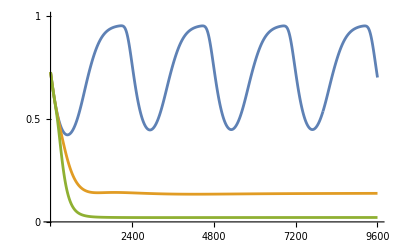

```mathematica
ListPlot[Join[{wt/60},tslist/60],Joined->True,Ticks->{{2400,4800,7200,9600},{0,0.5,1}},PlotRange->{{0,9600},{0,1}},AxesStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.005]]
```

CLOCK and BMAL1 WT overexpression

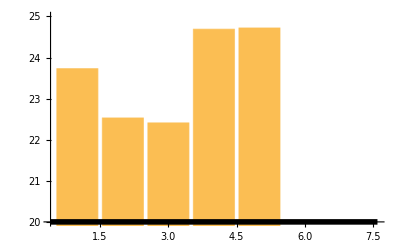

```mathematica
BarChart[{23.73,22.53,22.41,24.69,24.72,0,0},Ticks->{Automatic,{20,21,22,23,24,25}},AxesStyle->Directive[Black,Thickness[0.01]],PlotRange->{20,25}]
```